Data. Columns: Vcc (actual), ADC0 (temp), ADC1 (voltage)

```mathematica
data=Import["~/src/xbee_temp_sensor/calibration/vinvout.csv"];TableForm[data]
```

2.562 | 4619 | 3416
2.832 | 4615 | 3769
3.013 | 4409 | 3957
3.234 | 4392 | 3840
3.506 | 4388 | 4280
4.04 | 4282 | 4800
4.23 | 4248 | 5136
4.49 | 4184 | 6144
4.74 | 4112 | 7488
5.01 | 4088 | 8064
5.24 | 4128 | 8112
5.52 | 6144 | 8172

Actual VREF (measured)

```mathematica
vref=1221;
```

Voltage divider coefficient. I have 2 resistors 40K and 10K. Actual coefficient should be 4, but measuring voltages V_cc/V_adc1 I got:

```mathematica
k=4.0/0.796
```

5.02513

Convert RAW ADC value to volts:

```mathematica
raw2volts[x_] := x/8*vref/1024
```

Plot ADC1 raw value (measured voltage, y-axis) vs. actual V_cc (x-axis)

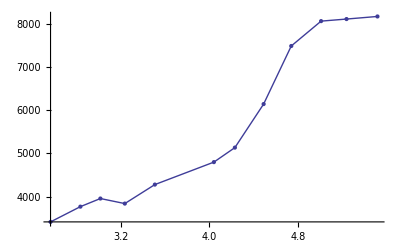

```mathematica
ListLinePlot[Transpose[{data[[All,1]],data[[All,3]]}],Mesh-> All]
```

Plot  estimated V_cc calculated from ADC1, y-axis vs. actual V_cc (x-axis)

```mathematica
evoltages=raw2volts[data[[All,3]]]*k/1000;
```

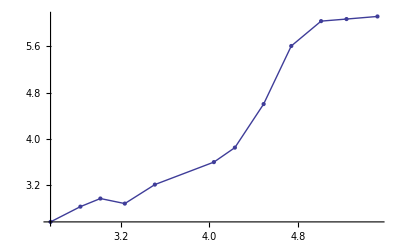

```mathematica
ListLinePlot[Transpose[{data[[All,1]],evoltages}],Mesh-> All]
```

Fit a 3rd degree polynomial to voltage estimation, to estimate actual voltage based on measures:

```mathematica
vf=Fit[Transpose[{evoltages,data[[All,1]]}],{1,v,v^2,v^3},v]
```

-12.4647+10.3012 v-2.14076 v^2+0.152242 v^3

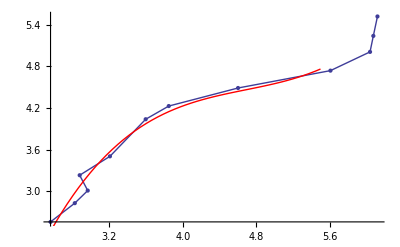

```mathematica
Show[ListLinePlot[Transpose[{evoltages,data[[All,1]]}],Mesh-> All],Plot[vf,{v,2.5,5.5},PlotStyle-> Red]]
```

Plot ADC0 raw value (measured temp, y-axis) vs. V_cc (x-axis). The tempearute around 20C during the experiment.

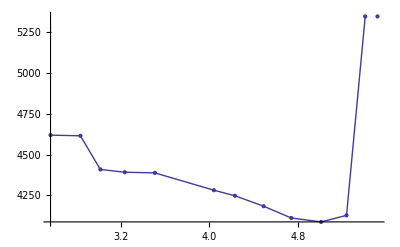

```mathematica
ListLinePlot[Transpose[{data[[All,1]],data[[All,2]]}],Mesh-> All]
```

Plot estimated temperature (y-axis) vs V_cc(x-axis)

```mathematica
etemps=(raw2volts[data[[All,2]]] - 500)/10;
```

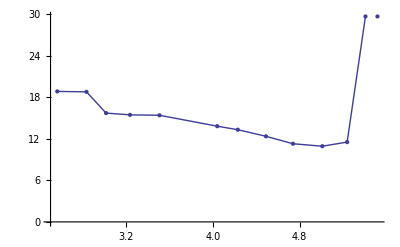

```mathematica
p1=ListLinePlot[Transpose[{data[[All,1]],etemps}],Mesh-> All,AxesOrigin-> {2.5,0}]
```

It looks like depenency is linear up to 5.0V.  We will assume V_cc operating range 0-5V.

```mathematica
etemps5 = Select[Transpose[{data[[All,1]],etemps}],#[[1]]<5&];
```

And  fit:

```mathematica
tf=Fit[etemps5,{1,va},va]
```

26.7787-3.24716 va

Assume true temp was measured around 3.3V

```mathematica
truetemp= tf/. va-> 3.3
```

16.063

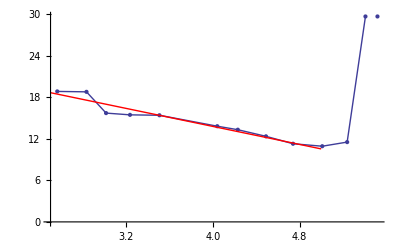

```mathematica
Show[p1,Plot[tf,{va,2.5,5},PlotStyle-> Red]]
```

Let us come up with correction function:

```mathematica
itf=-tf[[2]]+truetemp-tf[[1]]
```

-10.7156+3.24716 va

All together now:

Corrected voltages:

```mathematica
cvoltages=Map[vf /. v-> #&,evoltages]
```

{2.42736,2.97998,3.22464,3.07621,3.57353,3.97434,4.14946,4.44137,4.82935,5.20233,5.24278,5.29566}

Temp corrections:

```mathematica
tcorr = Map[itf/. va-> # &, cvoltages]
```

{-2.83361,-1.03916,-0.244713,-0.726694,0.888186,2.18968,2.75834,3.70622,4.96605,6.17718,6.30853,6.48022}

Corrected Temps

```mathematica
ctemps = etemps+tcorr
```

{16.0116,17.7464,15.4705,14.7351,16.2904,16.012,16.0739,16.0678,16.2545,17.1079,17.8355,48.0552}

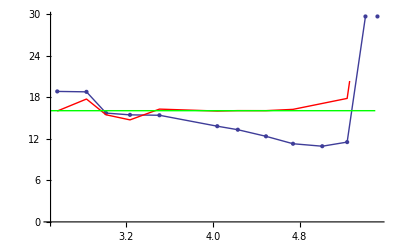

```mathematica
Show[p1,ListLinePlot[Transpose[{data[[All,1]],ctemps}],PlotStyle->Red],
Plot[truetemp,{x,2.5,5.5},PlotStyle->Green]]
```